```mathematica
(* List of fast Deleglise-Rivat alpha factors for x ≤ 10^21 found by running pi(x) benchmarks using the find_fastest_alpha.sh script *)

alphaDelegliseRivat =  { (* {x, alpha} *) {1, 1}, {10^1, 1}, {10^2, 1},{10^3, 1},{10^4, 1},{10^5, 1},{10^6,1.172}, {10^7,1.561},{10^8,1.865},{10^9,2.255},{10^10,2.854},{10^11,4.365}, {10^12,7.422}, {10^13, 10.164},  {10^14, 12.806}, {10^15,  20.604}, {10^16, 29.676}, {10^17, 51.527}, {10^18,62.914} , {10^19,68.930}}
```

{{1,1},{10,1},{100,1},{1000,1},{10000,1},{100000,1},{1000000,1.172},{10000000,1.561},{100000000,1.865},{1000000000,2.255},{10000000000,2.854},{100000000000,4.365},{1000000000000,7.422},{10000000000000,10.164},{100000000000000,12.806},{1000000000000000,20.604},{10000000000000000,29.676},{100000000000000000,51.527},{1000000000000000000,62.914},{10000000000000000000,68.93}}

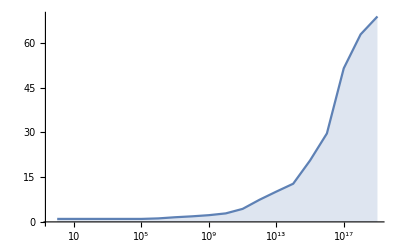

```mathematica
ListLogLinearPlot[alphaDelegliseRivat,Filling->Bottom, Joined-> True]
```

```mathematica
(* alpha is a tuning factor that balances the compuation of the easy special leaves and the hard special leaves. The formula below is used in the file src/primesum.cpp to calculate a fast alpha factor for the computation of pi(x). *)

NonlinearModelFit[alphaDelegliseRivat, a(Log[x])^3 + b (Log[x])^2 + c Log[x] + d, {a,b, c, d}, x]
```

FittedModel[-0.5712+0.964706 Log[x]-0.0975921 («1»)^2+0.00261288 Log[x]^3]

```mathematica
%3["BestFit"]
```

-0.5712+0.964706 Log[x]-0.0975921 Log[x]^2+0.00261288 Log[x]^3

```mathematica
StyleBox[
   RowBox[{"(*", " ", 
    RowBox[{
    "alpha", " ", "is", " ", "a", " ", "tuning", " ", "factor", " ", "that", 
     " ", "balances", " ", "the", " ", "compuation", " ", "of", " ", "the", 
     " ", "easy", " ", "special", " ", "leaves", " ", "and", " ", "the", " ", 
     "hard", " ", "special", " ", 
     RowBox[{"leaves", ".", " ", "The"}], " ", "formula", " ", "below", " ", 
     "is", " ", "used", " ", "in", " ", "the", " ", "file", " ", 
     RowBox[{"src", "/", 
      RowBox[{"primesum", ".", "cpp"}]}], " ", "to", " ", "calculate", " ", 
     "a", " ", "fast", " ", "alpha", " ", "factor", " ", "for", " ", "the", 
     " ", "computation", " ", "of", " ", "pi", 
     RowBox[{
      RowBox[{"(", "x", ")"}], "."}]}], " ", "*)"}],
   FontColor->GrayLevel[0.5]], "\[IndentingNewLine]", "\[IndentingNewLine]", 
  RowBox[{"NonlinearModelFit", "[", 
   RowBox[{"alphaDelegliseRivatLarge", ",", " ", 
    RowBox[{
     RowBox[{"a", 
      RowBox[{
       RowBox[{"(", 
        RowBox[{"Log", "[", "x", "]"}], ")"}], "^", "3"}]}], " ", "+", " ", 
     RowBox[{"b", " ", 
      RowBox[{
       RowBox[{"(", 
        RowBox[{"Log", "[", "x", "]"}], ")"}], "^", "2"}]}], " ", "+", " ", 
     RowBox[{"c", " ", 
      RowBox[{"Log", "[", "x", "]"}]}], " ", "+", " ", "d"}], ",", " ", 
    RowBox[{"{", 
     RowBox[{"a", ",", "b", ",", " ", "c", ",", " ", "d"}], "}"}], ",", " ", 
    "x"}], "]"}]}]], "Input",
 CellChangeTimes->{{3.652799964217605*^9, 3.65279997584527*^9}, {
   3.652893869904131*^9, 3.6528938753327827`*^9}, 3.652894046755538*^9}],

Cell[BoxData[
 TagBox[
  RowBox[{"FittedModel"
```

[", 
   TagBox[
    PanelBox[
     TagBox[
      RowBox[{"0.5919722020156437`", "\[VeryThinSpace]", "+", 
       RowBox[{"0.2821387363161177`", " ", 
        RowBox[{"Log", "[", "x", "]"}]}], "-", 
       RowBox[{"0.03757054349225608`", " ", 
        SuperscriptBox[
         RowBox[{"Log", "[", "x", "]"}], "2"]}], "+", 
       RowBox[{"0.0014906649828661817`", " ", 
        SuperscriptBox[
         RowBox[{"Log", "[", "x", "]"}], "3"]}]}],
      Short[#, 2]& ],
     FrameMargins->5],
    Editable -> False], "]"}],
  InterpretTemplate[
  FittedModel[{
    "Nonlinear", {$CellContext`a -> 
      0.0014906649828661817`, $CellContext`b -> -0.03757054349225608, \
$CellContext`c -> 0.2821387363161177, $CellContext`d -> 
      0.5919722020156437}, {{$CellContext`x}, $CellContext`d + $CellContext`c 
       Log[$CellContext`x] + $CellContext`b 
       Log[$CellContext`x]^2 + $CellContext`a Log[$CellContext`x]^3}}, {
    1}, {{1, 1}, {10, 1}, {100, 1}, {1000, 1}, {10000, 1}, {100000, 1}, {
     1000000, 1.172}, {10000000, 1.861}, {100000000, 2.778}, {
     10000000000, 5.426}, {100000000000, 7.795}, {1000000000000, 10.96}, {
     10000000000000, 15.22}, {10000000000000000, 34.8}, {
     100000000000000000000, 79.68}, {1000000000000000000000, 96.86}, {
     10000000000000000000000, 109.61}, {100000000000000000000000, 130.33}, {
     1000000000000000000000000, 154.69}}, 
    Function[Null, 
     Internal`LocalizedBlock[{$CellContext`a, $CellContext`b, $CellContext`c, \
$CellContext`d, $CellContext`x}, #], {HoldAll}]]& ],
  Editable->False,
  SelectWithContents->True,
  Selectable->True]], "Output",
 CellFrame->{{0, 0}, {2, 0}},
 CellChangeTimes->{{3.652893519062272*^9, 3.652893531685191*^9}, 
   3.6528936557056828`*^9}]
}, Open  ]],

Cell[BoxData[
 RowBox[{
  StyleBox

```mathematica
*", " ", 
    RowBox[{
     RowBox[{
     "Below", " ", "is", " ", "another", " ", "formula", " ", "which", " ", 
      "is", " ", "quite", " ", "accurate", " ", "for", " ", "calculating", 
      " ", "the", "\[IndentingNewLine]", " ", "Deleglise"}], "-", 
     RowBox[{"Rivat", " ", "alpha", " ", "factor", " ", "in", " ", 
      RowBox[{"primesum", ".", " ", "The"}], " ", "constant", " ", "2200", 
      " ", "has", "\[IndentingNewLine]", " ", "been", " ", "obtained", " ", 
      "by", " ", "running", " ", "many", " ", "pi", 
      RowBox[{"(", 
       RowBox[{"10", "^", "20"}], ")"}], " ", 
      RowBox[{"benchmarks", "."}]}]}], " ", "*)"}],
   FontColor->GrayLevel[0.5]], "\[IndentingNewLine]", "\[IndentingNewLine]", 
  RowBox[{
   RowBox[{"alpha", "[", "x_", "]"}], " ", ":=", " ", 
   RowBox[{
    RowBox[{
     RowBox[{"(", 
      RowBox[{"Log", "[", "x", "]"}], ")"}], "^", "3"}], " ", "/", " ", 
    RowBox[{"(", 
     RowBox[{"2200", " ", 
      RowBox[{
       RowBox[{"(", 
        RowBox[{
         RowBox[{"Log", "[", 
          RowBox[{"Log", "[", 
           RowBox[{"10", "^", "20"}], "]"}], "]"}], " ", "/", " ", 
         RowBox[{"Log", "[", 
          RowBox[{"Log", "[", "x", "]"}], "]"}]}], ")"}], "^", "3"}]}], 
     ")"}]}]}]}]], "Input",
 CellFrame->{{0, 0}, {2, 0}},
 CellChangeTimes->{{3.6527997811174803`*^9, 3.652799782144432*^9}, 
   3.652800031367243*^9}],

Cell[CellGroupData[{

Cell[BoxData[
 RowBox[{
```

```mathematica
*", " ", 
    RowBox[{
     RowBox[{"List", " ", "of", " ", "fast", " ", "Lagarias"}], "-", "Miller",
      "-", 
     RowBox[{
     "Odlyzko", " ", "alpha", " ", "factors", " ", "found", " ", "by", " ", 
      "running", " ", "pi", 
      RowBox[{"(", "x", ")"}], " ", 
      RowBox[{"benchmarks", "."}]}]}], " ", "*)"}],
   FontColor->GrayLevel[0.5]], "\[IndentingNewLine]", "\[IndentingNewLine]", 
  RowBox[{"alphaLMO", " ", "=", " ", 
   RowBox[{"{", 
    StyleBox[
     RowBox[{"(*", " ", 
      RowBox[{"{", 
       RowBox[{"x", ",", " ", "alpha"}], "}"}], " ", "*)"}],
     FontColor->GrayLevel[0.5]], " ", 
    RowBox[{
     RowBox[{"{", 
      RowBox[{"1", ",", " ", "1"}], "}"}], ",", 
     RowBox[{"{", 
      RowBox[{
       RowBox[{"10", "^", "10"}], ",", " ", "1.208"}], "}"}], ",", " ", 
     RowBox[{"{", 
      RowBox[{
       RowBox[{"10", "^", "11"}], ",", " ", "1.281"}], "}"}], ",", "  ", 
     RowBox[{"{", 
      RowBox[{
       RowBox[{"10", "^", "12"}], ",", " ", "1.364"}], "}"}], ",", 
     RowBox[{"{", 
      RowBox[{
       RowBox[{"10", "^", "13"}], ",", " ", "1.679"}], "}"}], ",", 
     RowBox[{"{", 
      RowBox[{
       RowBox[{"10", "^", "14"}], ",", " ", "1.890"}], "}"}], ",", 
     RowBox[{"{", 
      RowBox[{
       RowBox[{"10", "^", "15"}], ",", "2.011"}], "}"}], ",", 
     RowBox[{"{", 
      RowBox[{
       RowBox[{"10", "^", "16"}], ",", " ", "2.113"}], "}"}], ",", 
     RowBox[{"{", 
      RowBox[{
       RowBox[{"10", "^", "17"}], ",", " ", "2.359"}], "}"}], ",", 
     RowBox[{"{", 
      RowBox[{
       RowBox[{"10", "^", "18"}], ",", " ", "2.556"}], "}"}]}], 
    "}"}]}]}]], "Input",
 CellChangeTimes->{{3.63421344494037*^9, 3.634213445624035*^9}, {
   3.634215431555122*^9, 3.634215513284093*^9}, {3.634215600175366*^9, 
   3.634215619788096*^9}, 3.634215656990878*^9, 3.634215720809465*^9, {
   3.6342157667969522`*^9, 3.634215767165007*^9}, {3.634215844568947*^9, 
   3.634215848768384*^9}, {3.634215892499003*^9, 3.6342158991052933`*^9}, {
   3.6342159486720448`*^9, 3.634215967468809*^9}, {3.634216242103594*^9, 
   3.634216251921739*^9}, 3.634217349492552*^9, {3.634314695950554*^9, 
   3.6343147086478233`*^9}, 3.634322609691835*^9, {3.6343231672555017`*^9, 
   3.634323170063471*^9}, 3.6343232738673983`*^9, {3.634323441217924*^9, 
   3.6343234449257107`*^9}, {3.634404012629353*^9, 3.6344040279052*^9}, {
   3.634405024424403*^9, 3.634405024582734*^9}, {3.6345813154704723`*^9, 
   3.63458132685883*^9}, {3.652340017483922*^9, 3.652340090042877*^9}, {
   3.6523401226925707`*^9, 3.6523401631045513`*^9}, {3.652340205179083*^9, 
   3.6523402578472652`*^9}, {3.652340388683112*^9, 3.652340400128792*^9}, 
   3.652340486932126*^9, {3.6523432960802717`*^9, 3.652343320573119*^9}, {
   3.652343353095994*^9, 3.652343375283201*^9}, {3.652358670776546*^9, 
   3.652358671261818*^9}, {3.652359327963564*^9, 3.6523593575432653`*^9}, {
   3.652799391654447*^9, 3.6527994077294073`*^9}, {3.652799459199575*^9, 
   3.6527994601652946`*^9}, {3.652894051835206*^9, 3.652894053576467*^9}}],

Cell[BoxData[
 RowBox[{"{", 
  RowBox[{
   Row
```

[{"{", 
    RowBox[{"1", ",", "1"}], "}"}], ",", 
   RowBox[{"{", 
    RowBox[{"10000000000", ",", "1.208`"}], "}"}], ",", 
   RowBox[{"{", 
    RowBox[{"100000000000", ",", "1.281`"}], "}"}], ",", 
   RowBox[{"{", 
    RowBox[{"1000000000000", ",", "1.364`"}], "}"}], ",", 
   RowBox[{"{", 
    RowBox[{"10000000000000", ",", "1.679`"}], "}"}], ",", 
   RowBox[{"{", 
    RowBox[{"100000000000000", ",", "1.89`"}], "}"}], ",", 
   RowBox[{"{", 
    RowBox[{"1000000000000000", ",", "2.011`"}], "}"}], ",", 
   RowBox[{"{", 
    RowBox[{"10000000000000000", ",", "2.113`"}], "}"}], ",", 
   RowBox[{"{", 
    RowBox[{"100000000000000000", ",", "2.359`"}], "}"}], ",", 
   RowBox[{"{", 
    RowBox[{"1000000000000000000", ",", "2.556`"}], "}"}]}], "}"}]], "Output",\

 CellChangeTimes->{3.634314739347858*^9, 3.634314868414618*^9, 
  3.6343204789205093`*^9, 3.6343234526147013`*^9, 3.63440502607679*^9, 
  3.634405625871414*^9, 3.652340498952908*^9, 3.652343380359654*^9, 
  3.6528000939680157`*^9}]
}, Open  ]],

Cell[CellGroupData[{

Cell[BoxData

```mathematica
RowBox[{"alphaLMO", ",", 
   RowBox[{"Filling", "\[Rule]", "Bottom"}], ",", " ", 
   RowBox[{"Joined", "\[Rule]", " ", "True"}]}], "]"}]], "Input",
 CellChangeTimes->{{3.6343148187325907`*^9, 3.6343148346924543`*^9}, 
   3.634323448934331*^9, 3.634403977189968*^9}],

Cell[BoxData[
 GraphicsBox[{{}, 
   GraphicsCo
```

exBox[{{0., 1.}, {23.025850929940457`, 1.208}, {
    25.328436022934504`, 1.281}, {27.631021115928547`, 1.364}, {
    29.933606208922594`, 1.679}, {32.23619130191664, 1.89}, {
    34.538776394910684`, 2.011}, {36.841361487904734`, 2.113}, {
    39.14394658089878, 2.359}, {41.44653167389282, 2.556}, {0., 0.}, {
    41.44653167389282, 0.}}, {{{}, 
      {RGBColor[0.368417, 0.506779, 0.709798], Opacity[0.2], EdgeForm[None], 
       GraphicsGroupBox[
        PolygonBox[{{1, 11, 12, 10, 9, 8, 7, 6, 5, 4, 3, 
         2}}]]}, {}, {}}, {{}, {}, 
      {RGBColor[0.368417, 0.506779, 0.709798], PointSize[
       0.012833333333333334`], AbsoluteThickness[1.6], 
       LineBox[{1, 2, 3, 4, 5, 6, 7, 8, 9, 10}]}}}], {}},
  AspectRatio->NCache[GoldenRatio^(-1), 0.6180339887498948],
  Axes->{True, True},
  AxesLabel->{None, None},
  AxesOrigin->{-1.5245631768066048`, 0},
  CoordinatesToolOptions:>{"DisplayFunction" -> ({
      Exp[
       Part[#, 1]], 
      Part[#, 2]}& ), "CopiedValueFunction" -> ({
      Exp[
       Part[#, 1]], 
      Part[#, 2]}& )},
  DisplayFunction->Identity,
  Frame->{{False, False}, {False, False}},
  FrameLabel->{{None, None}, {None, None}},
  FrameTicks->{{Automatic, Automatic}, {
     Charting`ScaledTicks[{Log, Exp}], 
     Charting`ScaledFrameTicks[{Log, Exp}]}},
  GridLines->{None, None},
  GridLinesStyle->Directive[
    GrayLevel[0.5, 0.4]],
  Method->{},
  PlotRange->{{-0.8634694098727672, 41.44653167389282}, {0, 2.556}},
  PlotRangeClipping->True,
  PlotRangePadding->{{
     Scaled[0.02], 
     Scaled[0.02]}, {
     Scaled[0.02], 
     Scaled[0.05]}},
  Ticks->FrontEndValueCache[{
     Charting`ScaledTicks[{Log, Exp}], Automatic}, {{{0., 
       FormBox["1", TraditionalForm], {0.01, 0.}, {
        AbsoluteThickness[0.1]}}, {9.210340371976184, 
       FormBox[
        TemplateBox[{"10", "4"}, "Superscript", SyntaxForm -> SuperscriptBox],
         TraditionalForm], {0.01, 0.}, {
        AbsoluteThickness[0.1]}}, {18.420680743952367`, 
       FormBox[
        TemplateBox[{"10", "8"}, "Superscript", SyntaxForm -> SuperscriptBox],
         TraditionalForm], {0.01, 0.}, {
        AbsoluteThickness[0.1]}}, {27.631021115928547`, 
       FormBox[
        TemplateBox[{"10", "12"}, "Superscript", SyntaxForm -> 
         SuperscriptBox], TraditionalForm], {0.01, 0.}, {
        AbsoluteThickness[0.1]}}, {36.841361487904734`, 
       FormBox[
        TemplateBox[{"10", "16"}, "Superscript", SyntaxForm -> 
         SuperscriptBox], TraditionalForm], {0.01, 0.}, {
        AbsoluteThickness[0.1]}}, {4.605170185988092, 
       FormBox[
        InterpretationBox[
         StyleBox[
          
          GraphicsBox[{}, ImageSize -> {0., 0.}, BaselinePosition -> 
           Baseline], "CacheGraphics" -> False], 
         Spacer[{0., 0.}]], TraditionalForm], {0.005, 0.}, {
        AbsoluteThickness[0.1]}}, {13.815510557964274`, 
       FormBox[
        InterpretationBox[
         StyleBox[
          
          GraphicsBox[{}, ImageSize -> {0., 0.}, BaselinePosition -> 
           Baseline], "CacheGraphics" -> False], 
         Spacer[{0., 0.}]], TraditionalForm], {0.005, 0.}, {
        AbsoluteThickness[0.1]}}, {23.025850929940457`, 
       FormBox[
        InterpretationBox[
         StyleBox[
          
          GraphicsBox[{}, ImageSize -> {0., 0.}, BaselinePosition -> 
           Baseline], "CacheGraphics" -> False], 
         Spacer[{0., 0.}]], TraditionalForm], {0.005, 0.}, {
        AbsoluteThickness[0.1]}}, {32.23619130191664, 
       FormBox[
        InterpretationBox[
         StyleBox[
          
          GraphicsBox[{}, ImageSize -> {0., 0.}, BaselinePosition -> 
           Baseline], "CacheGraphics" -> False], 
         Spacer[{0., 0.}]], TraditionalForm], {0.005, 0.}, {
        AbsoluteThickness[0.1]}}, {41.44653167389282, 
       FormBox[
        InterpretationBox[
         StyleBox[
          GraphicsBox[{}, ImageSize -> {0., 0.}, BaselinePosition -> 
           Baseline], "CacheGraphics" -> False], 
         Spacer[{0., 0.}]], TraditionalForm], {0.005, 0.}, {
        AbsoluteThickness[0.1]}}}, Automatic}]]], "Output",
 CellChangeTimes->{3.6343148736908913`*^9, 3.634323454204451*^9, 
  3.6344039781488867`*^9, 3.6344050322068663`*^9, 3.652340509921791*^9, 
  3.652343393925089*^9, 3.652358378447218*^9, 3.652800095697736*^9}]
}, Open  ]],

Cell[BoxData[
 RowBox[{"\[Indentin

```mathematica
StyleBox[
   RowBox[{"(*", " ", 
    RowBox[{
    "alpha", " ", "is", " ", "a", " ", "tuning", " ", "factor", " ", "that", 
     " ", "balances", " ", "the", " ", "compuation", " ", "of", " ", "the", 
     " ", "easy", " ", "special", " ", "leaves", " ", "and", " ", "the", " ", 
     "hard", " ", "special", " ", 
     RowBox[{"leaves", ".", " ", "The"}], " ", "formula", " ", "below", " ", 
     "is", " ", "used", " ", "in", " ", "the", " ", "file", " ", 
     RowBox[{"src", "/", 
      RowBox[{"primesum", ".", "cpp"}]}], " ", "to", " ", "calculate", " ", 
     "a", " ", "fast", " ", "alpha", " ", "factor", " ", "for", " ", "the", 
     " ", "computation", " ", "of", " ", "pi", 
     RowBox[{
      RowBox[{"(", "x", ")"}], "."}]}], " ", "*)"}],
   FontColor->GrayLevel[0.5]]}]], "Input",
 CellChangeTimes->{{3.652359107254675*^9, 3.652359108209537*^9}, {
   3.652893880030965*^9, 3.652893884628096*^9}, 3.6528940589063597`*^9}],

Cell[CellGroupData[{

Cell[BoxData[
 RowBox[{"
```

```mathematica
RowBox[{"alphaLMO", ",", " ", 
   RowBox[{
    RowBox[{"a", 
     RowBox[{
      RowBox[{"(", 
       RowBox[{"Log", "[", "x", "]"}], ")"}], "^", "2"}]}], " ", "+", " ", 
    RowBox[{"b", "  ", 
     RowBox[{"Log", "[", "x", "]"}]}], " ", "+", " ", "c"}], ",", " ", 
   RowBox[{"{", 
    RowBox[{"a", ",", "b", ",", " ", "c"}], "}"}], ",", " ", "x"}], 
  "]"}]], "Input",
 CellChangeTimes->{{3.634216277450708*^9, 3.63421631260785*^9}, {
   3.634216345523642*^9, 3.634216356164029*^9}, {3.6343148016652737`*^9, 
   3.6343148100460567`*^9}, 3.634322645710272*^9, {3.634323063590989*^9, 
   3.634323065777611*^9}, 3.634323459263245*^9, {3.634323494476931*^9, 
   3.634323495748851*^9}}],

Cell[BoxData[
 TagBox[
  RowBox[{"FittedModel"
```

[", 
   TagBox[
    PanelBox[
     TagBox[
      RowBox[{"0.9909481657262896`", "\[VeryThinSpace]", "-", 
       RowBox[{"0.026141119143409816`", " ", 
        RowBox[{"Log", "[", "x", "]"}]}], "+", 
       RowBox[{"0.0015651182060183821`", " ", 
        SuperscriptBox[
         RowBox[{"Log", "[", "x", "]"}], "2"]}]}],
      Short[#, 2]& ],
     FrameMargins->5],
    Editable -> False], "]"}],
  InterpretTemplate[
  FittedModel[{
    "Nonlinear", {$CellContext`a -> 
      0.0015651182060183821`, $CellContext`b -> -0.026141119143409816`, \
$CellContext`c -> 
      0.9909481657262896}, {{$CellContext`x}, $CellContext`c + $CellContext`b 
       Log[$CellContext`x] + $CellContext`a Log[$CellContext`x]^2}}, {
    1}, {{1, 1}, {10000000000, 1.208}, {100000000000, 1.281}, {
     1000000000000, 1.364}, {10000000000000, 1.679}, {
     100000000000000, 1.89}, {1000000000000000, 2.011}, {
     10000000000000000, 2.113}, {100000000000000000, 2.359}, {
     1000000000000000000, 2.556}}, 
    Function[Null, 
     Internal`LocalizedBlock[{$CellContext`a, $CellContext`b, $CellContext`c, \
$CellContext`x}, #], {HoldAll}]]& ],
  Editable->False,
  SelectWithContents->True,
  Selectable->True]], "Output",
 CellFrame->{{0, 0}, {2, 0}},
 CellChangeTimes->{3.634216361898741*^9, 3.6343148963894043`*^9, 
  3.634320481245118*^9, 3.634322649079475*^9, 3.634323462345338*^9, 
  3.634323497831388*^9, 3.6344056317660627`*^9, 3.652340523756771*^9, 
  3.652343397994679*^9, 3.652358382254871*^9, 3.652800098796775*^9}]
}, Open  ]]
},
WindowSize->{838, 973},
WindowMar